```mathematica
Get[NotebookDirectory[]<>#]&/@{
"23_10_04_parameters_1.m",
"23_10_04_simulation_1.m",
"23_10_04_styles_1.m"
};
```

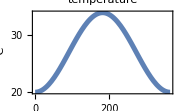

```mathematica
sinusmin=20;
sinusmax=34;
sinusmax2=30;
sinusshades={-100,-100};
wrange={w->{sinusmin-2,sinusmax+2}};
makesinusenvironment[min_,max_]:={w->Piecewise[{{min+(max-min)/2+(max-min)/2 Sin[3/2  π+(2 π)/365. t], True}, {0, True}}]};
environment=makesinusenvironment[sinusmin,sinusmax];
tempplot[environment,parvalsFvFmArr,Automatic]
```

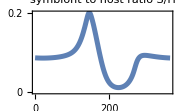

```mathematica
sol=simulate[parvalsFvFmArr/.environment,environment,fluxvars,inivalsdefault/.parvalsFvFmArr/.w->25];
partplot[
S/H,environment,parvalsFvFmArr,sol,{}]
```

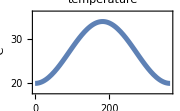
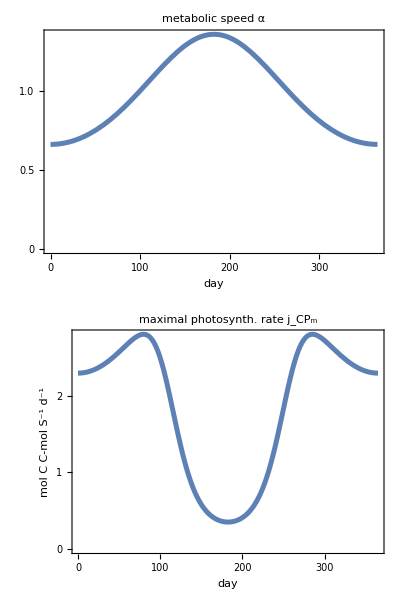
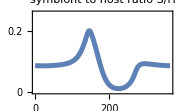
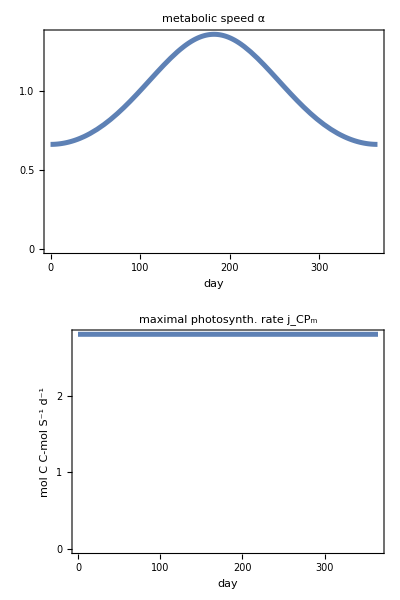
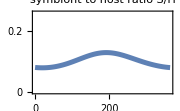
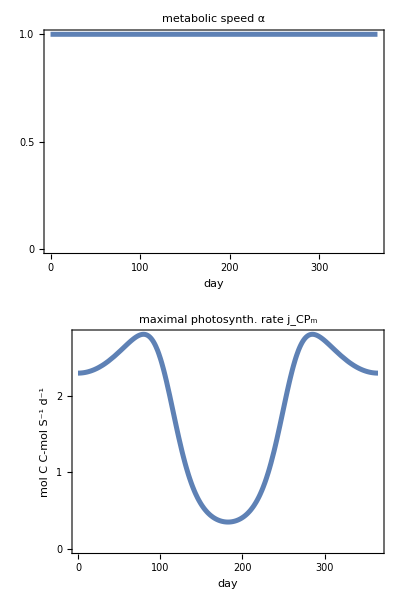
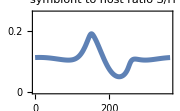
-Graphics- | -Graphics-
-Graphics- | -Graphics-
    
full model

-Graphics-
-Graphics-
-Graphics-
acceleration model

-Graphics-
-Graphics-
-Graphics-
damage model

-Graphics-
-Graphics-
-Graphics-

```mathematica
(Export[NotebookDirectory[]<>"export/"<>"simus-Short-All.pdf",#];#)&@Column[{Grid[{{arrow2,Column[{Framed[Column[{tempplot[makesinusenvironment[sinusmin,sinusmax],parvalsFvFmArr,w/.wrange]}],RoundingRadius->framingRadius],arrow1},Alignment->Center],arrow3}},Alignment->Bottom],
Row[(PanelPlotShort@@#)&/@{
{parvalsFvFmArr,makesinusenvironment[sinusmin,sinusmax],"full model"},
{parvalsArr,makesinusenvironment[sinusmin,sinusmax],"acceleration model"},
{parvalsFvFm,makesinusenvironment[sinusmin,sinusmax],"damage model"}
}, "  "]},Alignment->Center,Spacings->0]
```

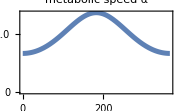
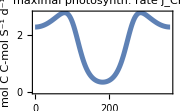
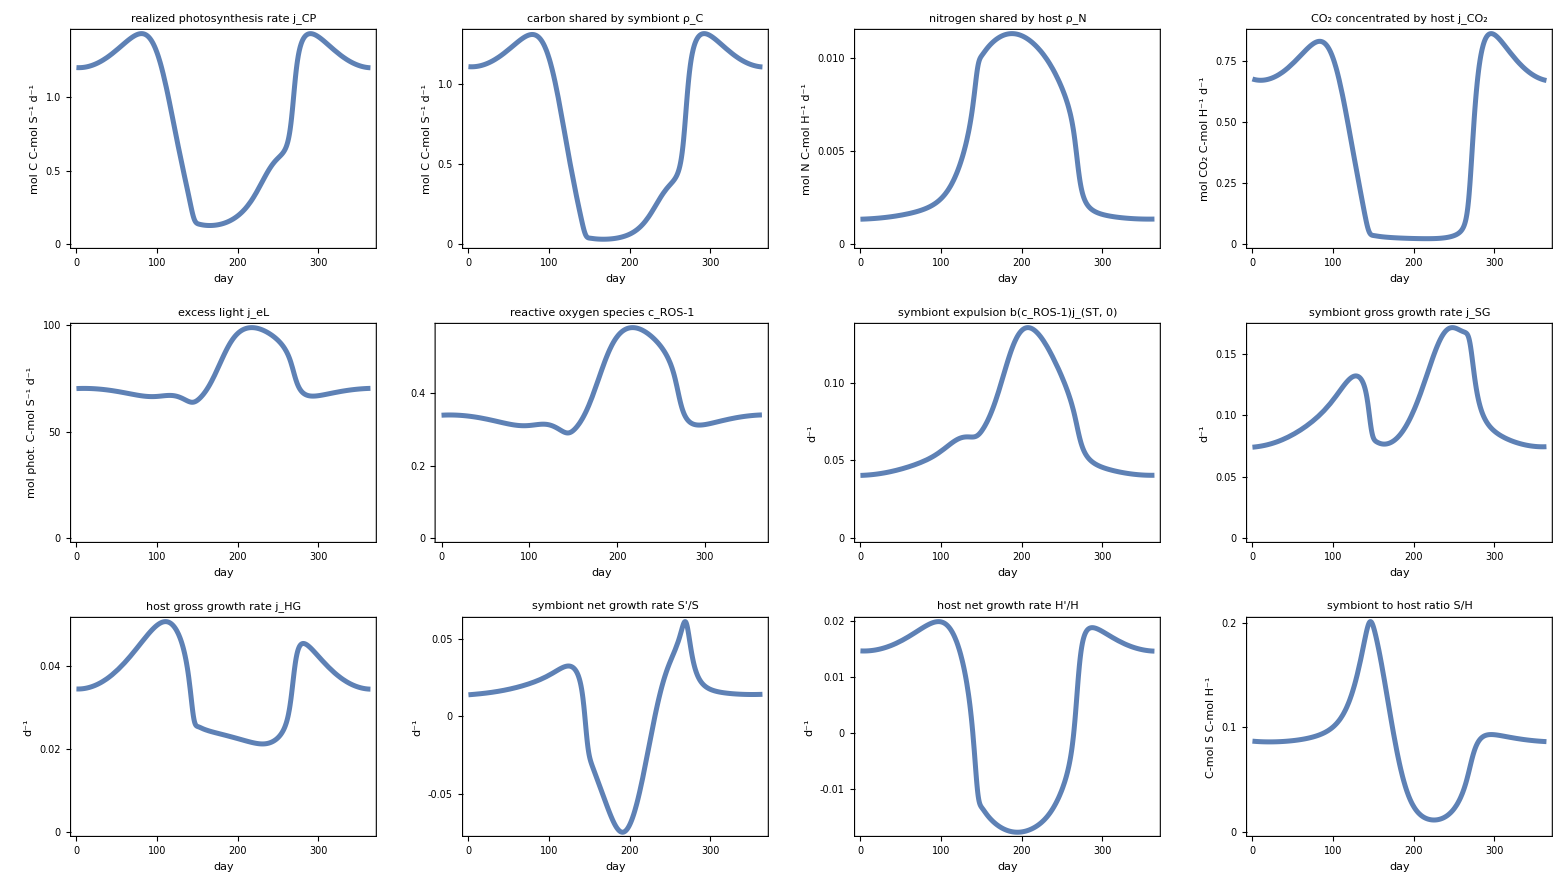
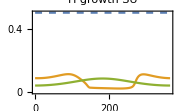
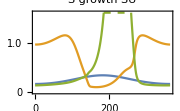
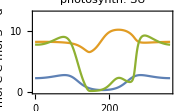
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
PWplot["simus-sinus-FvFm-Arr.pdf",parvalsFvFmArr,makesinusenvironment[sinusmin,sinusmax],Join[{H->#,S->.2#}&@(200{.005,1}),wrange,SUmaxs],sinusshades]
```

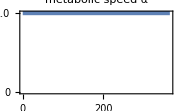
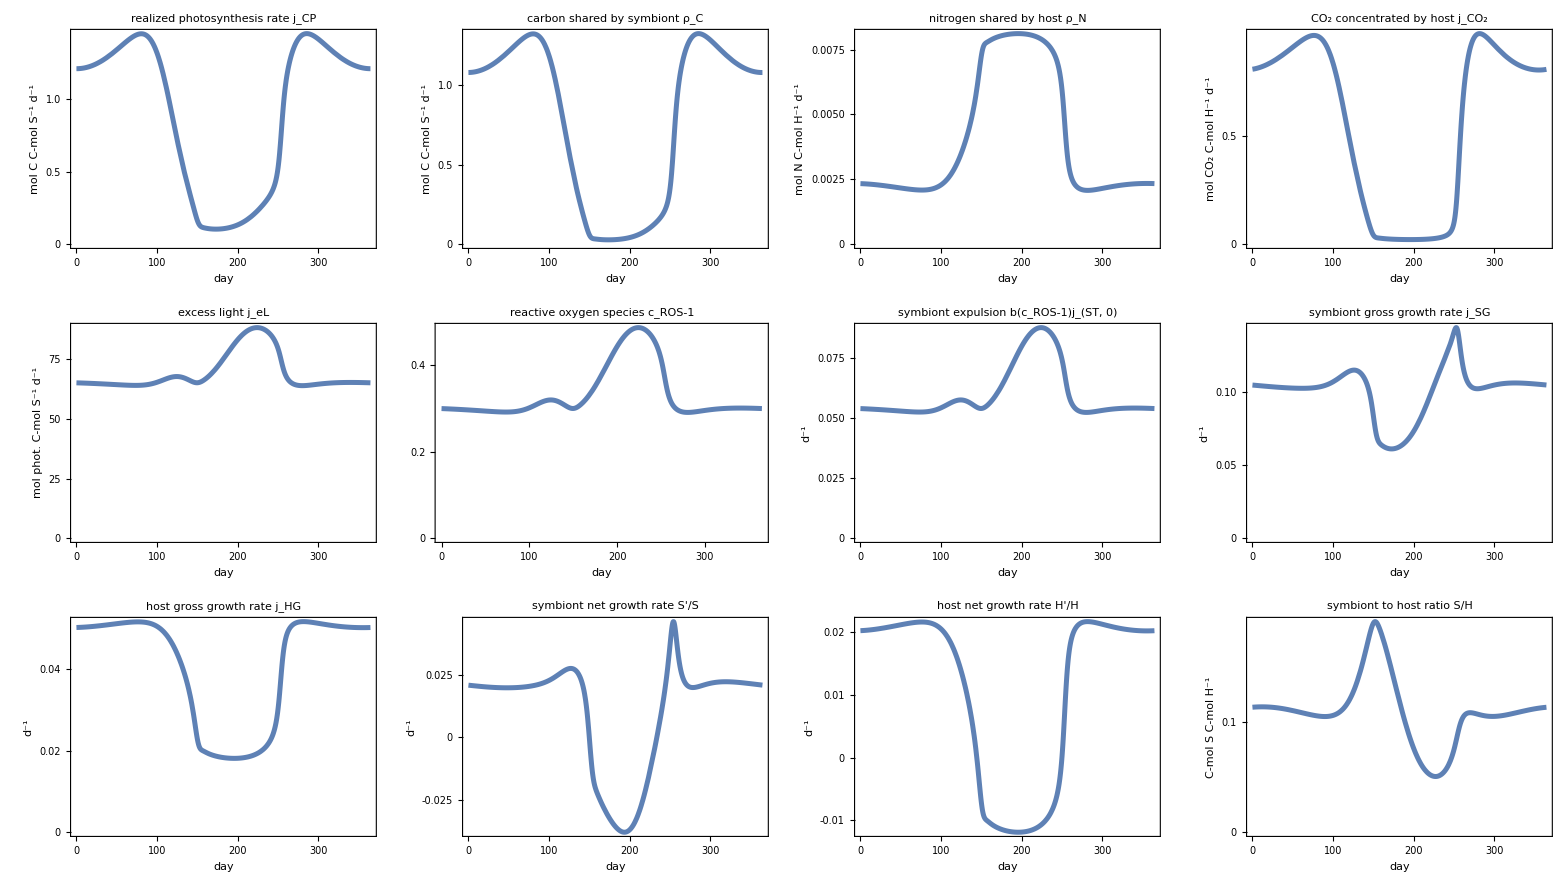
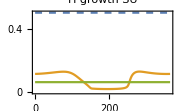
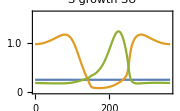
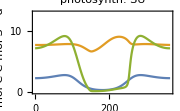
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
PWplot["simus-sinus-FvFm.pdf",parvalsFvFm,makesinusenvironment[sinusmin,sinusmax],Join[{H->#,S->.2#}&@(1{1,1000}),wrange,SUmaxs],sinusshades]
```

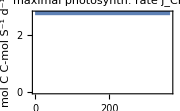
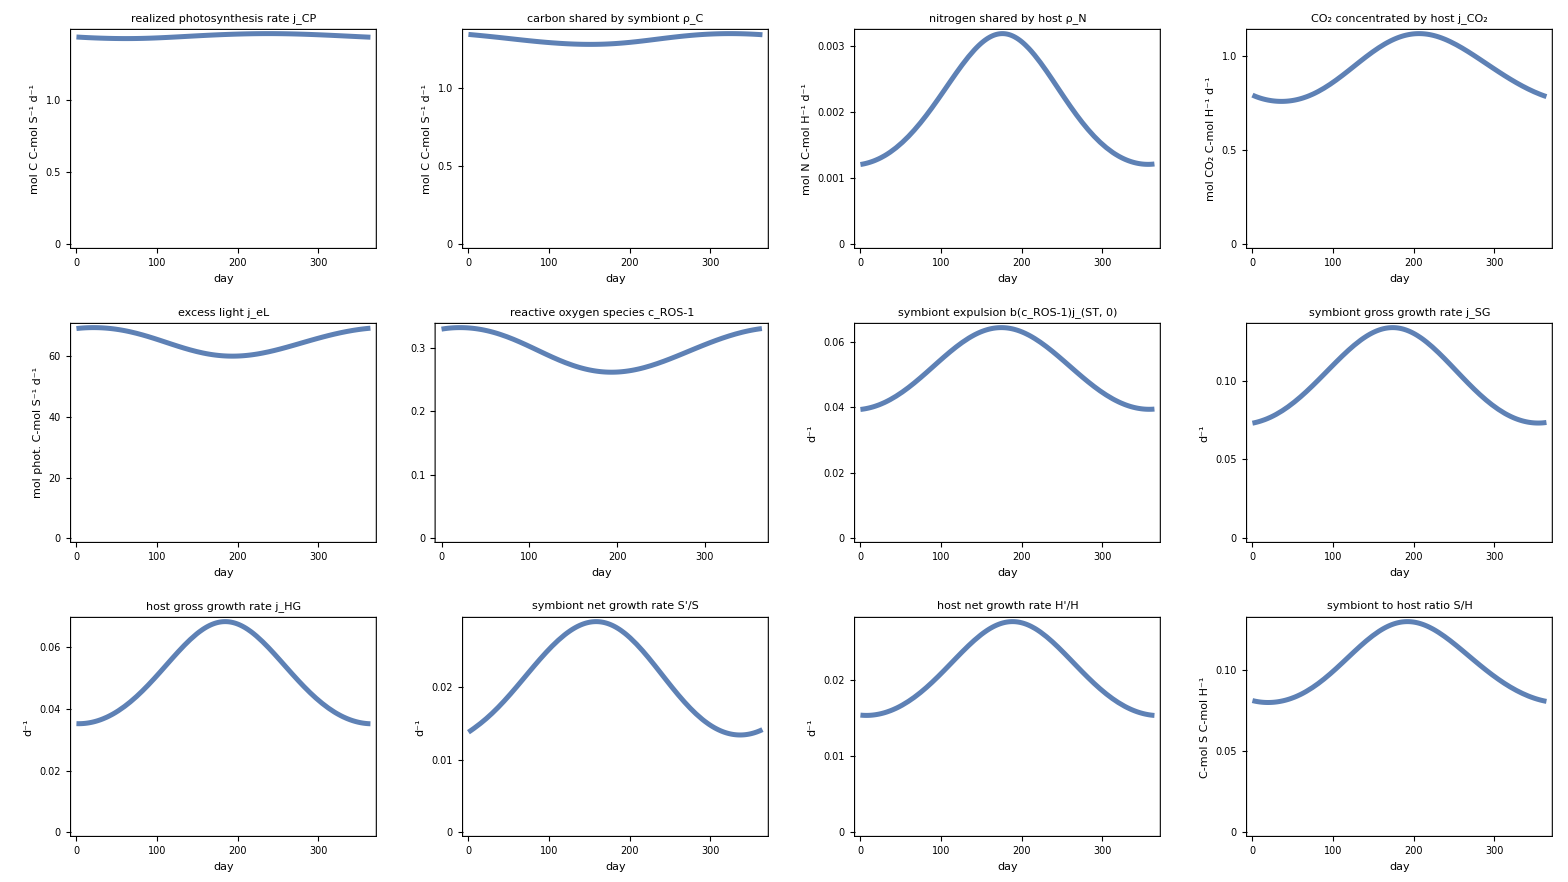
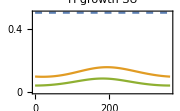
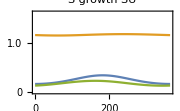
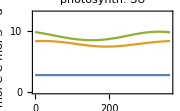
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
PWplot["simus-sinus-Arr.pdf",parvalsArr,makesinusenvironment[sinusmin,sinusmax],Join[{H->#,S->.2#}&@(100{10,10^5}),wrange,SUmaxs],sinusshades]
```

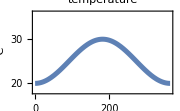
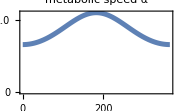
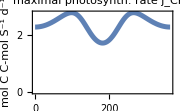
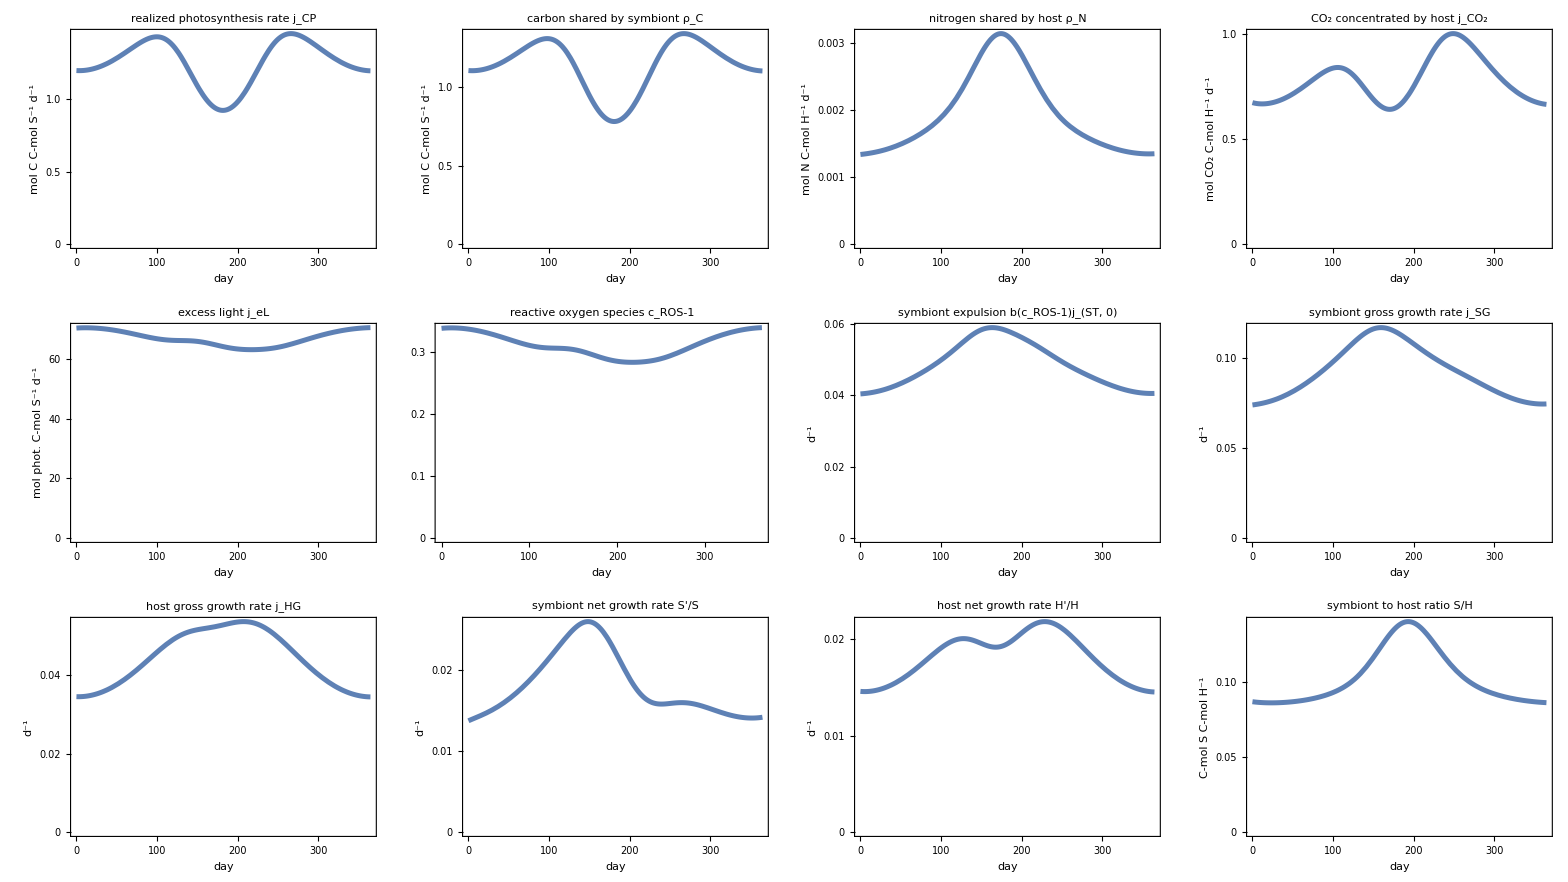
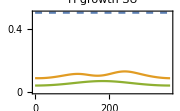
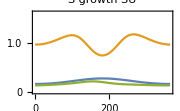
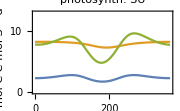
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

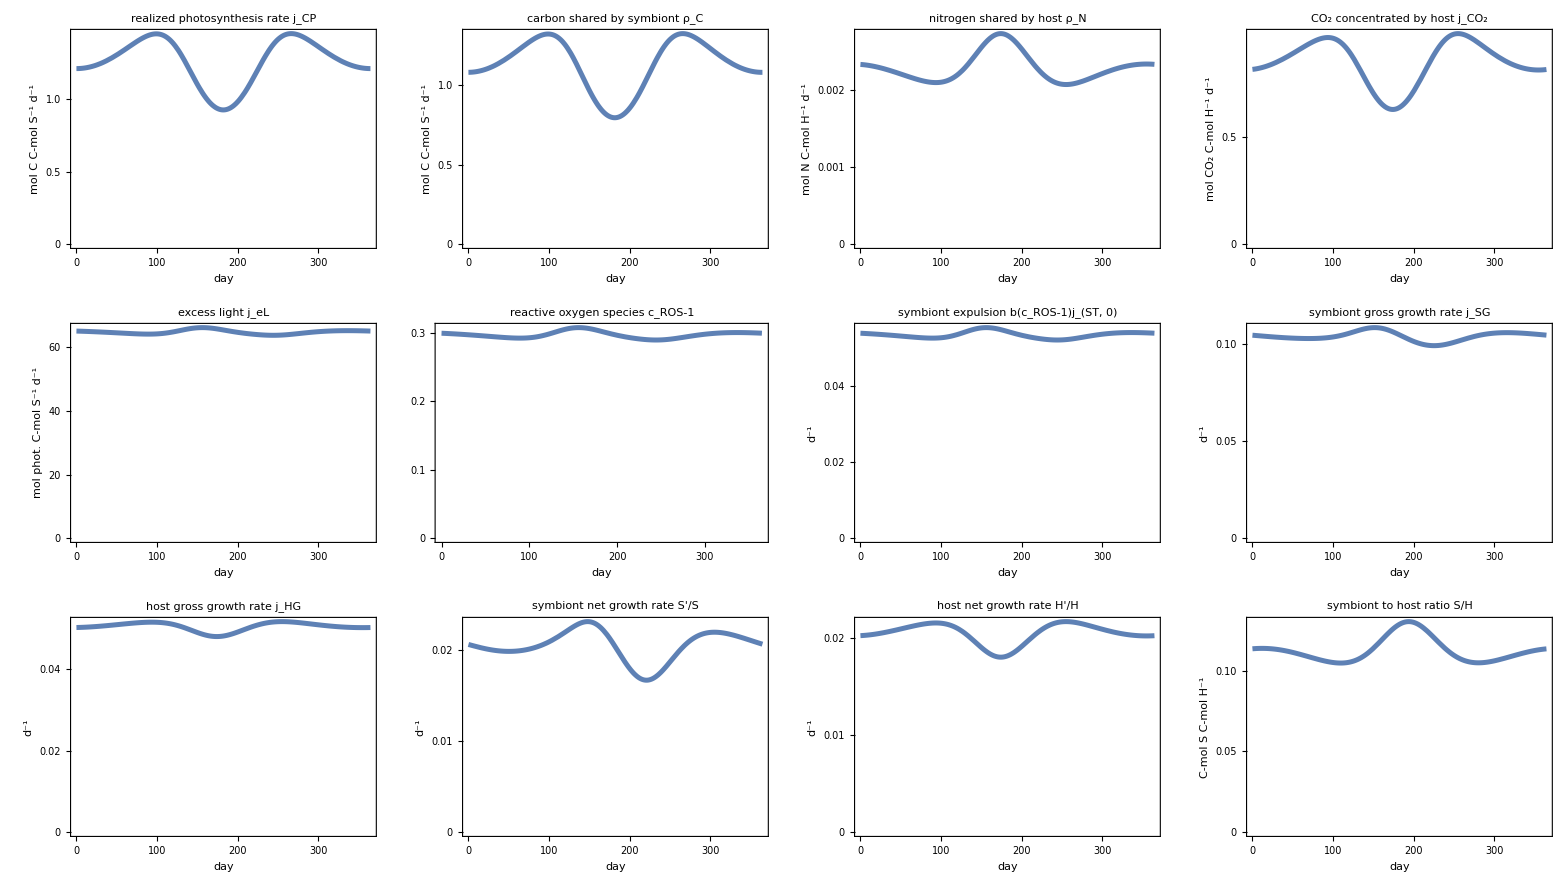
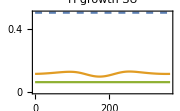
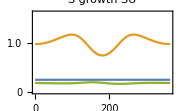
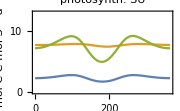
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

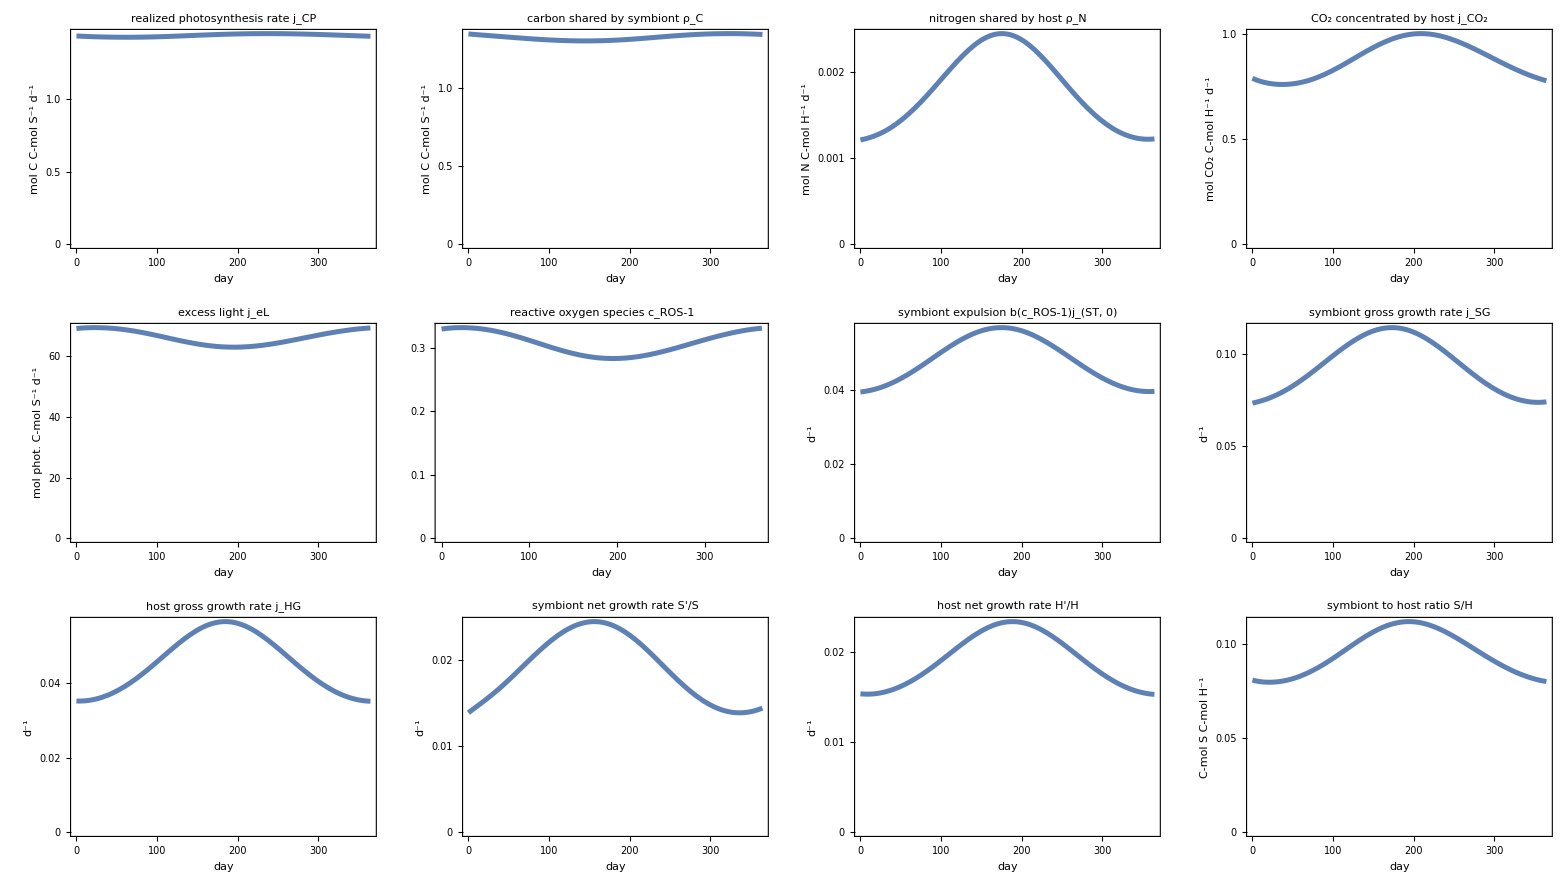
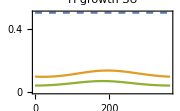
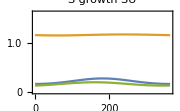
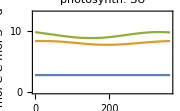
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
PWplot["simus-sinus-2-FvFm-Arr.pdf",parvalsFvFmArr,makesinusenvironment[sinusmin,sinusmax2],Join[{H->#,S->.2#}&@(10^7{.00005,1}),wrange,SUmaxs],sinusshades]
PWplot["simus-sinus-2-FvFm.pdf",parvalsFvFm,makesinusenvironment[sinusmin,sinusmax2],Join[{H->#,S->.2#}&@(10^7{.00005,1}),wrange,SUmaxs],sinusshades]
PWplot["simus-sinus-2-Arr.pdf",parvalsArr,makesinusenvironment[sinusmin,sinusmax2],Join[{H->#,S->.2#}&@(10^7{.00005,1}),wrange,SUmaxs],sinusshades]
```

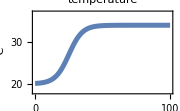
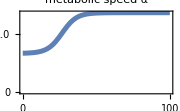
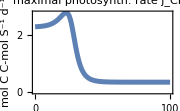
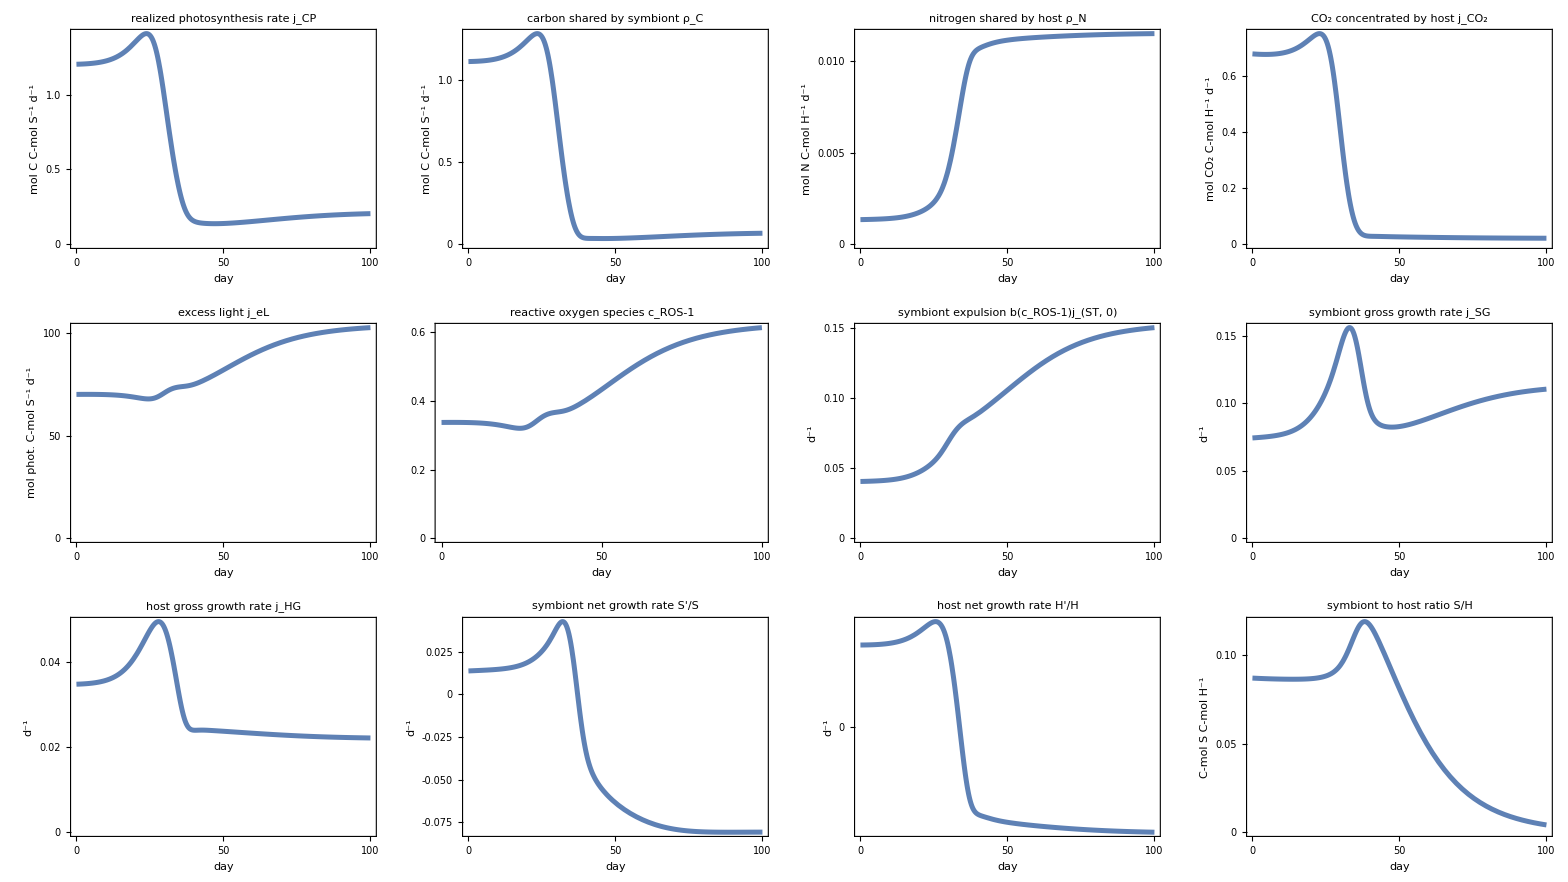
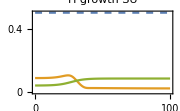
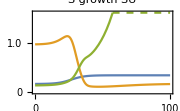
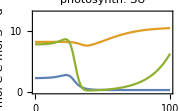
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

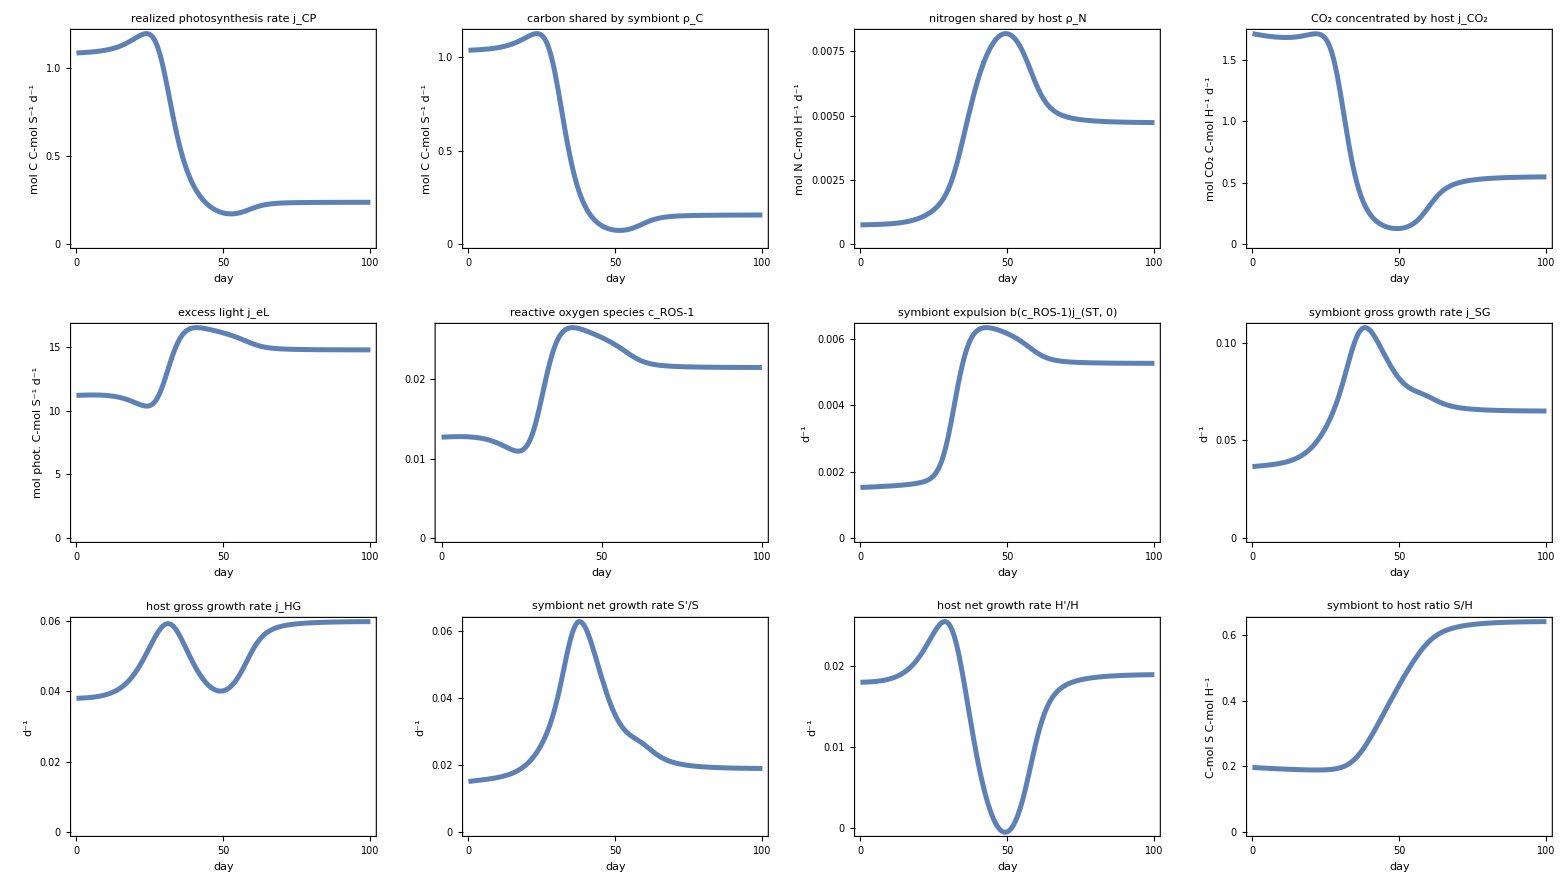
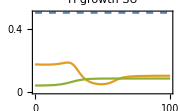
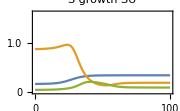
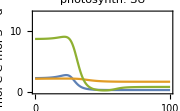
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
wrangepw={w->{18,37}};
environmentpw={w->20+14(1-sigmoidFunction /.{ED50->25,steepness->.2,w->t,sigmax->1})};
PWplot["simus-pw-FvFm-Arr.pdf",parvalsFvFmArr/.(tmax->_)->(tmax->100),environmentpw,Join[{H-> #,S-> .2# }&@({.5,50}),wrangepw,SUmaxs],{-100,-99}]
PWplot["simus-pw-high-S-H-FvFm-Arr.pdf",parvalsFvFmArr/.{(L->_)->(L->10),(tmax->_)->(tmax->100)},environmentpw,Join[{H-> #,S-> .2# }&@({1,100}),wrangepw,SUmaxs],{-100,-99}]
```

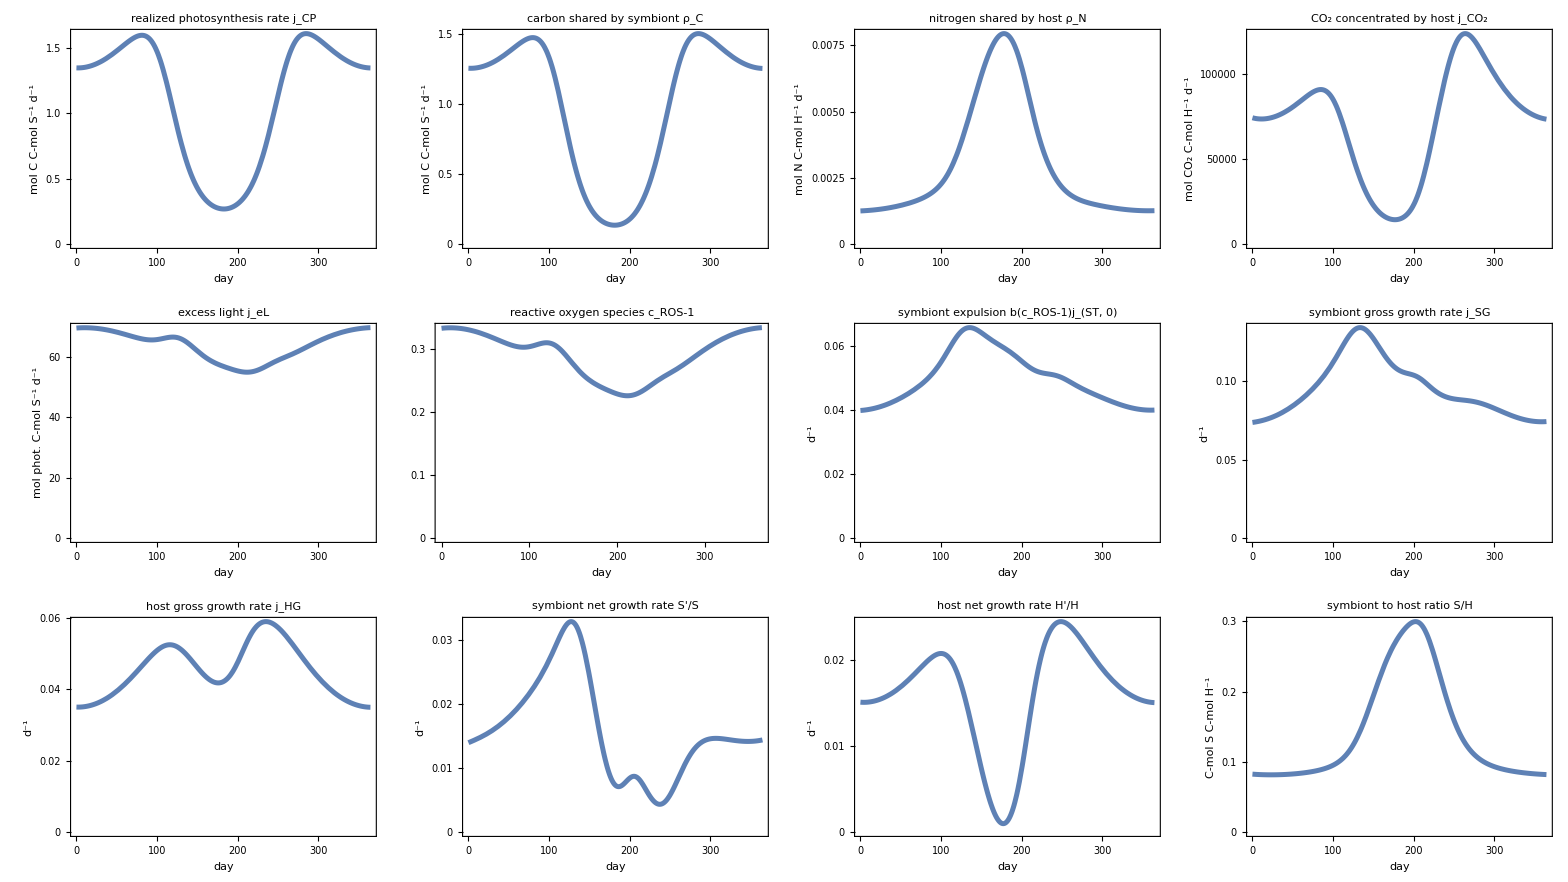
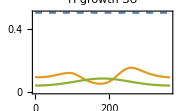
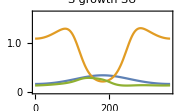
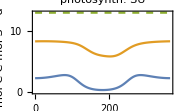
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

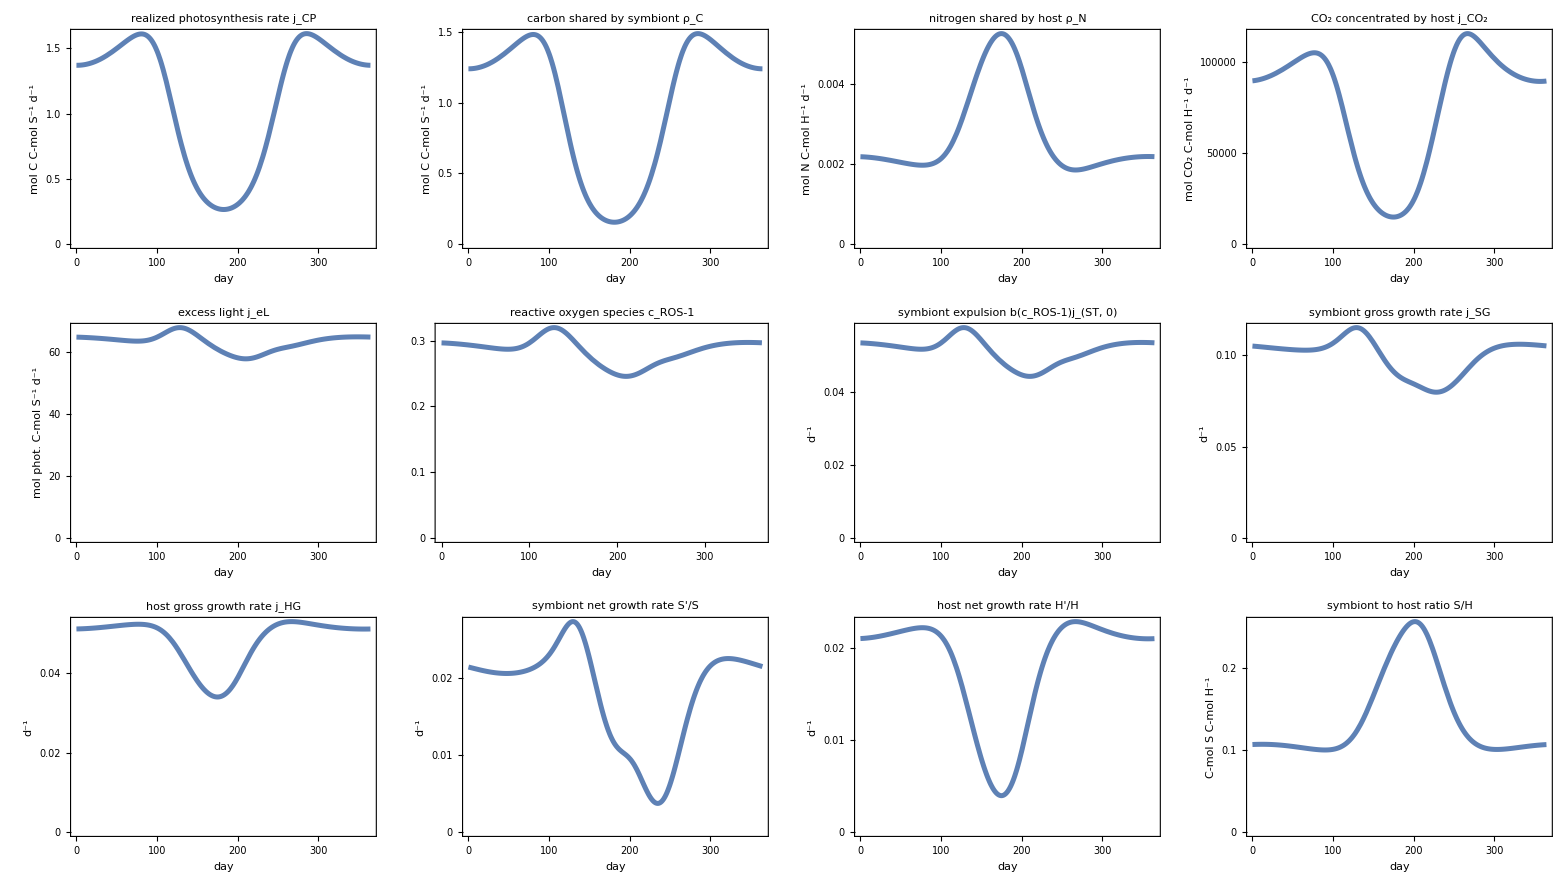
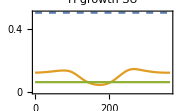
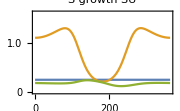
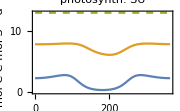
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

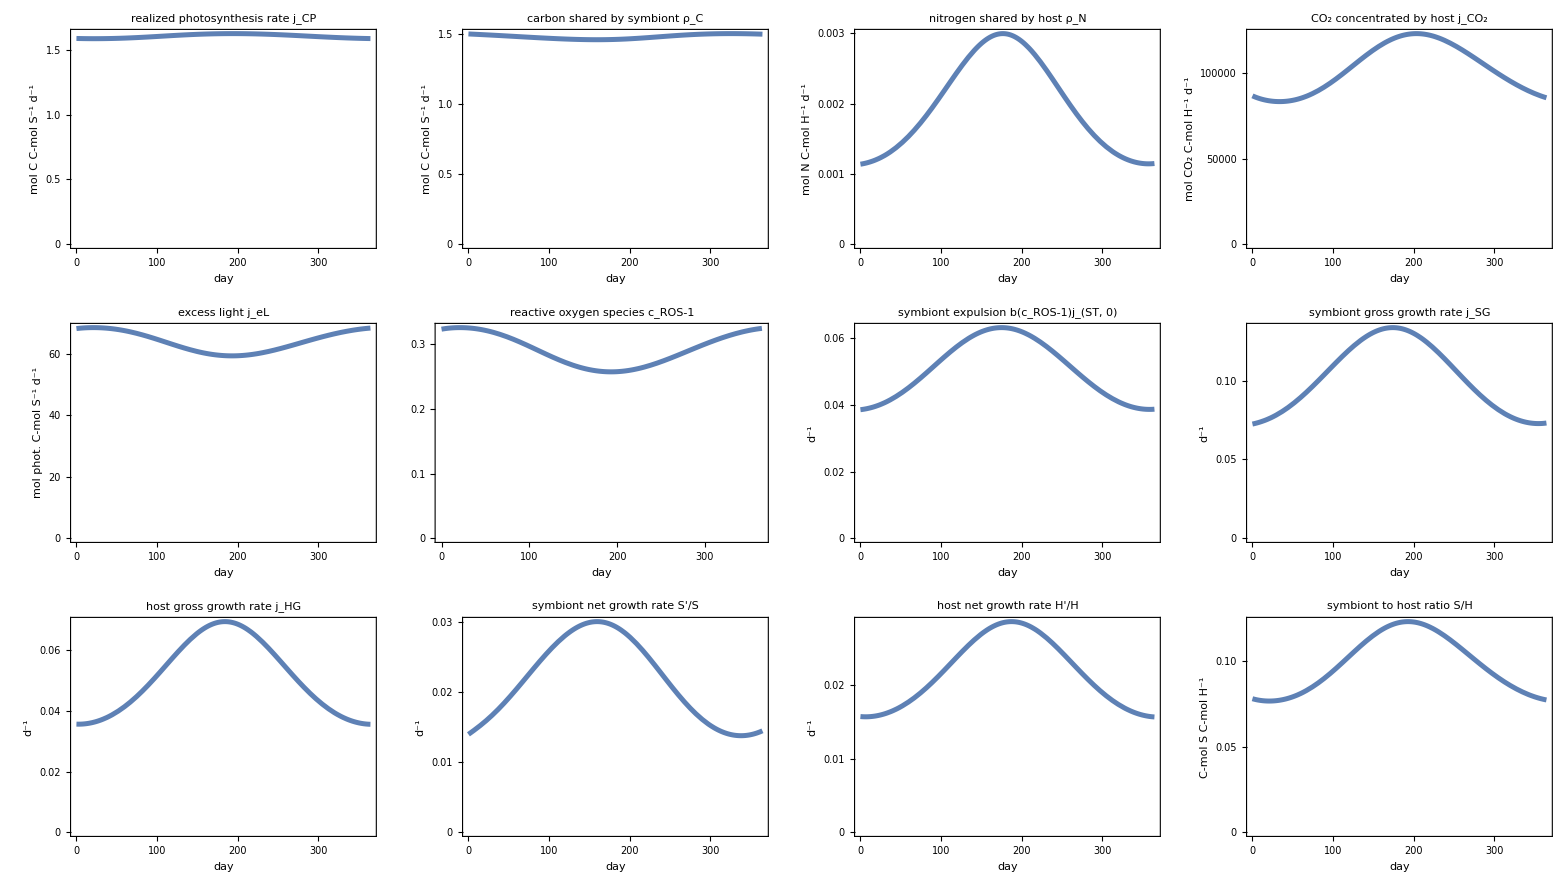
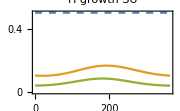
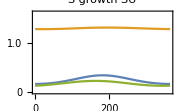
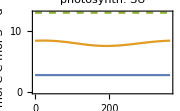
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
PWplot["simus-sinus-unlimited-CO2-FvFm-Arr.pdf",parvalsFvFmArr/.ReplacePars[{kCO2->10^6}],makesinusenvironment[sinusmin,sinusmax],Join[{H->#,S->.2#}&@(200{.005,1}),wrange,SUmaxs],sinusshades]
PWplot["simus-sinus-unlimited-CO2-FvFm.pdf",parvalsFvFm/.ReplacePars[{kCO2->10^6}],makesinusenvironment[sinusmin,sinusmax],Join[{H->#,S->.2#}&@(200{.005,1}),wrange,SUmaxs],sinusshades]
PWplot["simus-sinus-unlimited-CO2-Arr.pdf",parvalsArr/.ReplacePars[{kCO2->10^6}],makesinusenvironment[sinusmin,sinusmax],Join[{H->#,S->.2#}&@(200{.005,1}),wrange,SUmaxs],sinusshades]
```

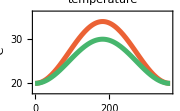
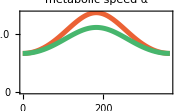
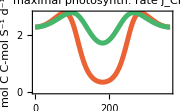
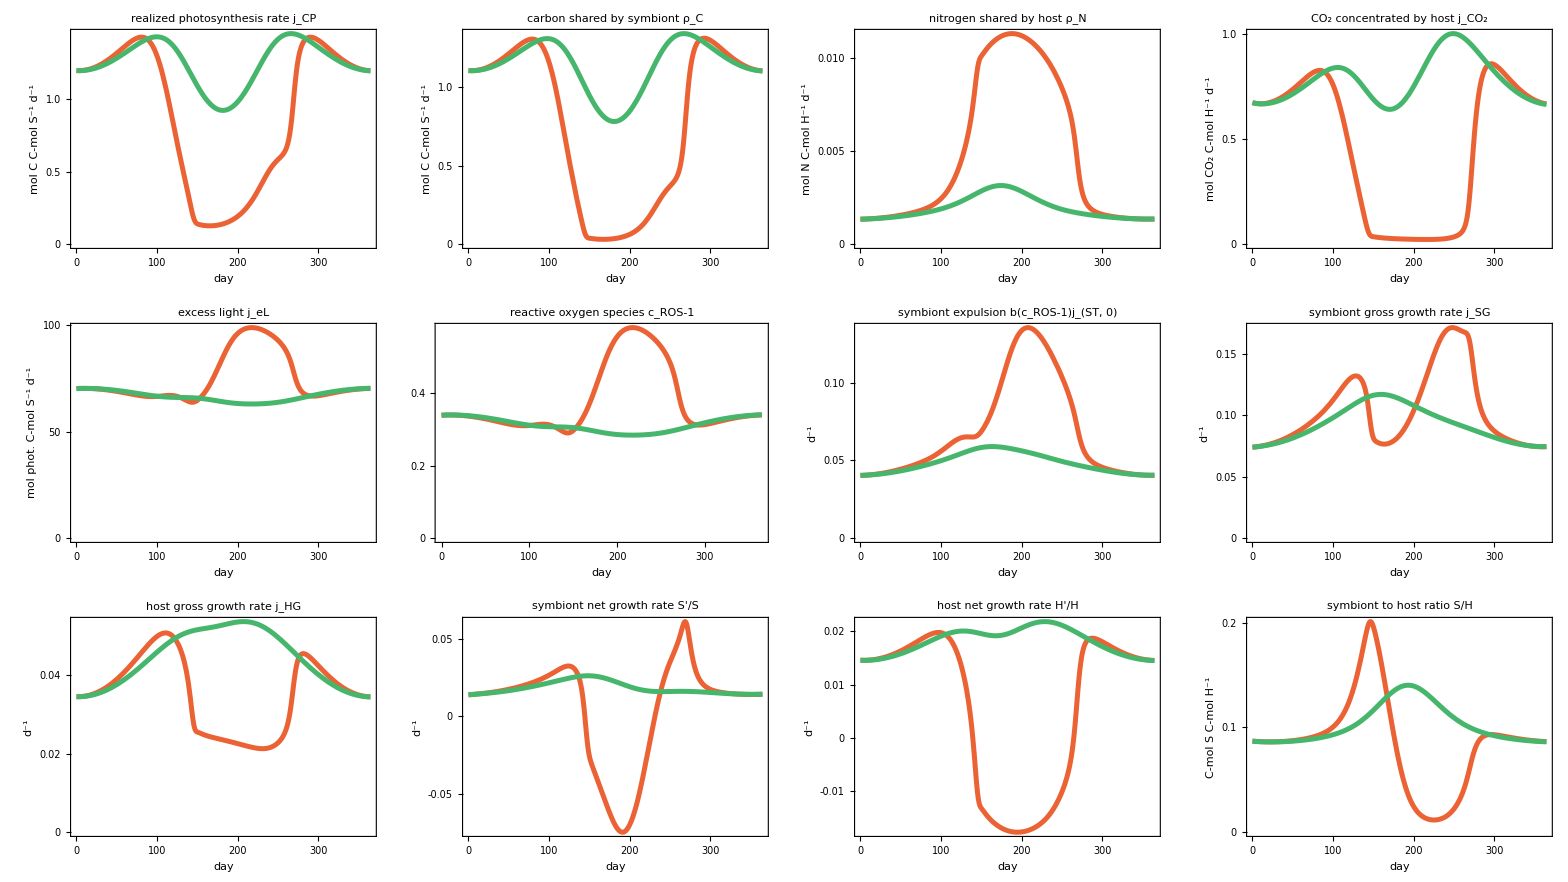
-Graphics-peak temperature
-Graphics- | 34°C
-Graphics- | 30°C
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-

```mathematica
(Export[NotebookDirectory[]<>"export/"<>"simus-sinus-FvFm-Arr-2-temperatures.pdf",#];#)&@PanelPlotMultipleRuns[toplot,parvalsFvFmArr,makesinusenvironment[sinusmin,#]&/@{sinusmax,sinusmax2},Evaluate@colorsmultsimus,inivalsdefault,{-100,-99},wrange,arrangementMultipleRuns]
```

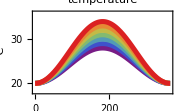
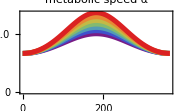
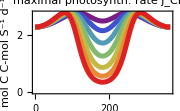
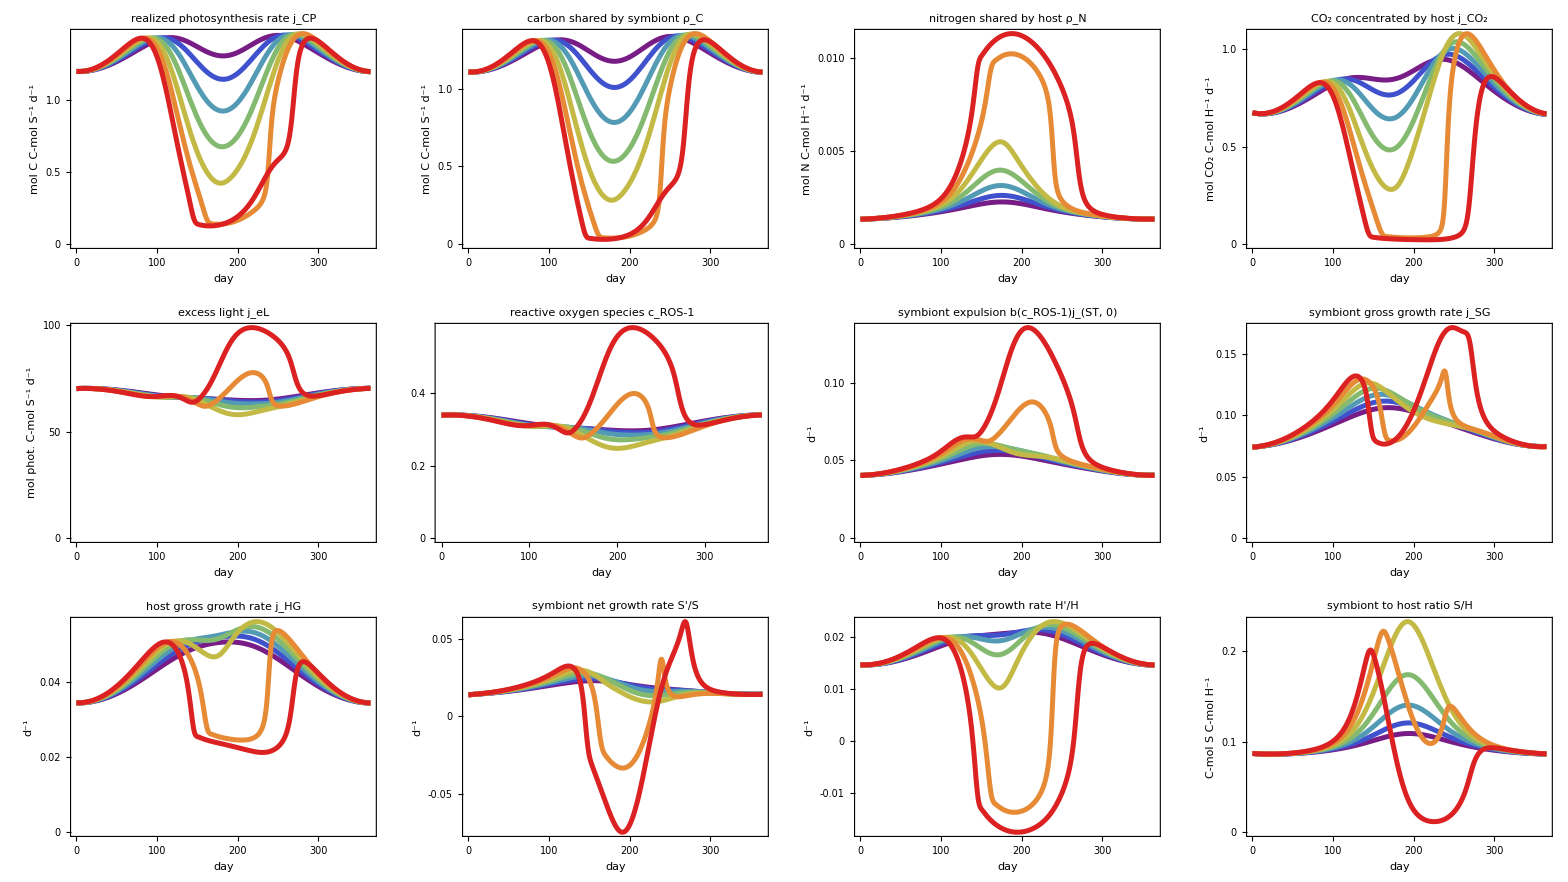
-Graphics-peak temperature
-Graphics- | 28°C
-Graphics- | 29°C
-Graphics- | 30°C
-Graphics- | 31°C
-Graphics- | 32°C
-Graphics- | 33°C
-Graphics- | 34°C
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-

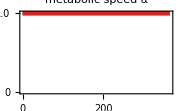
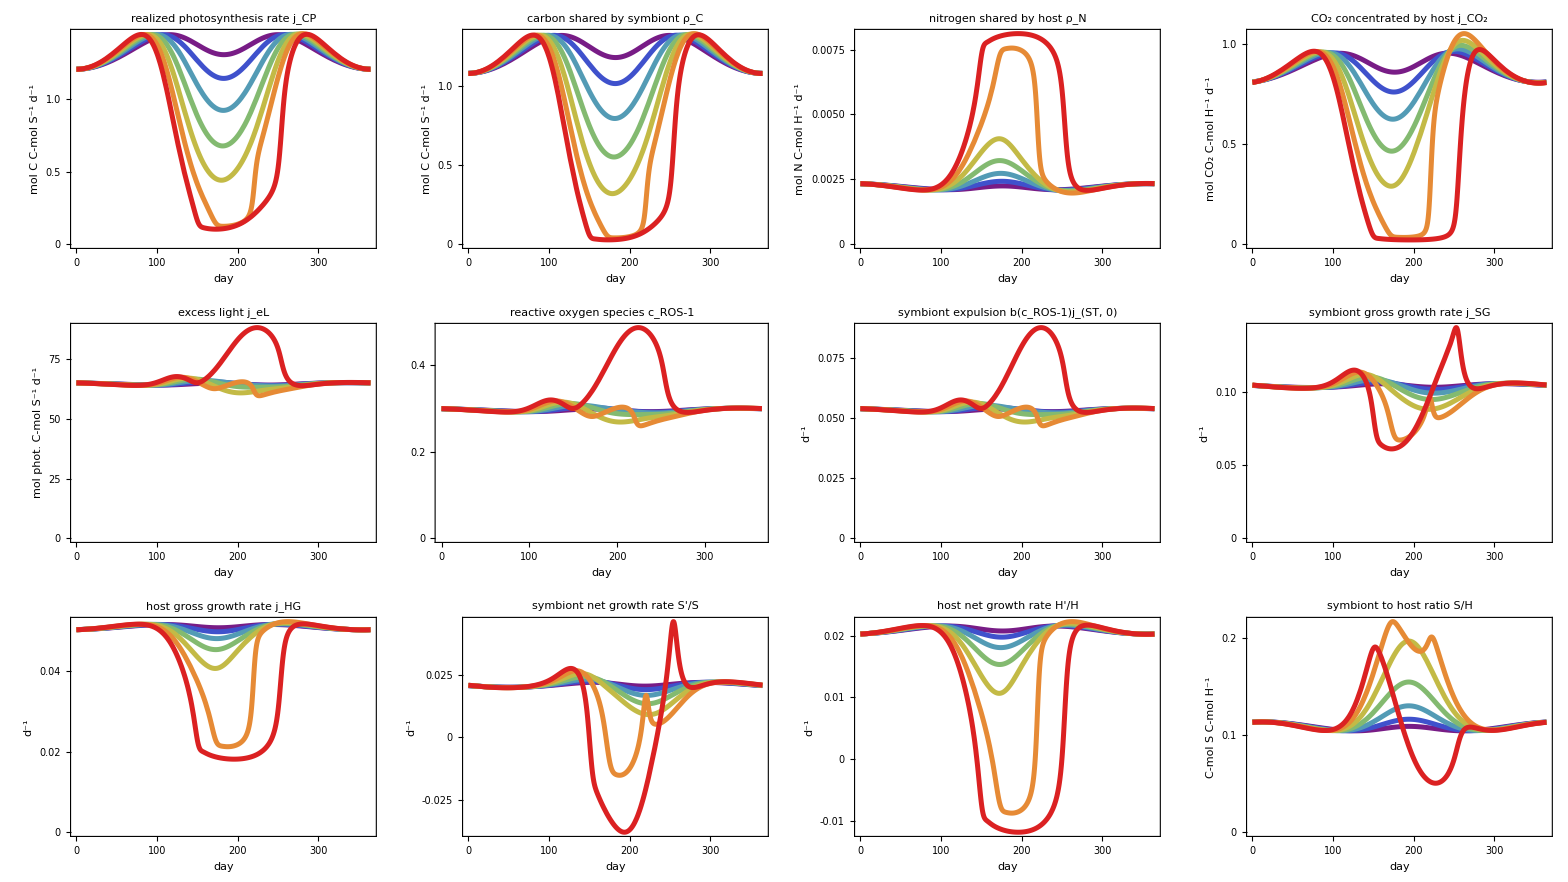
-Graphics-peak temperature
-Graphics- | 28°C
-Graphics- | 29°C
-Graphics- | 30°C
-Graphics- | 31°C
-Graphics- | 32°C
-Graphics- | 33°C
-Graphics- | 34°C
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-

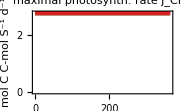
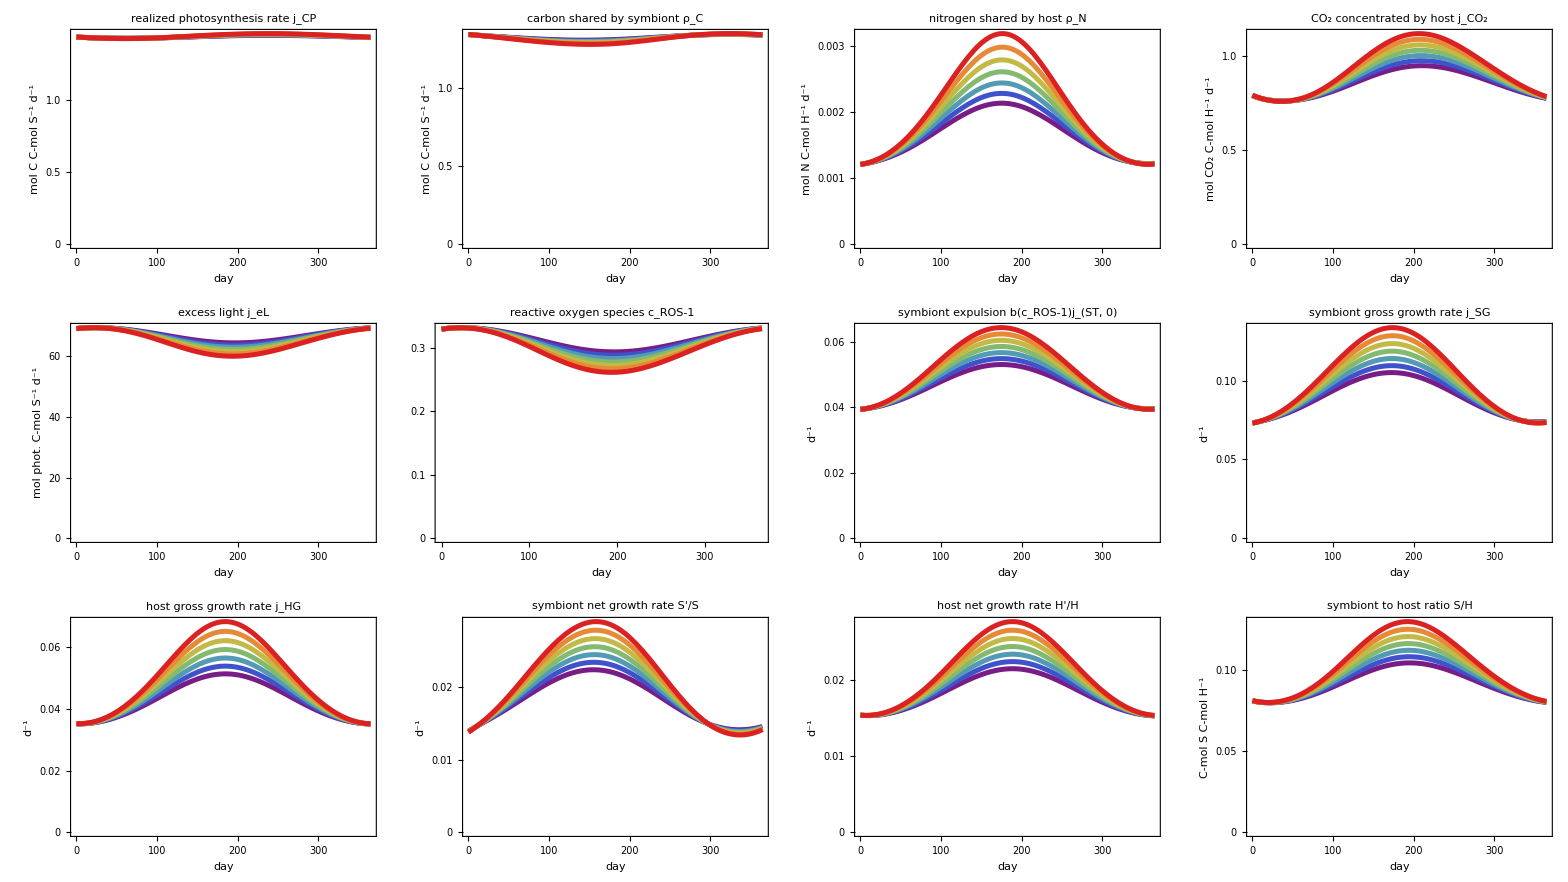
-Graphics-peak temperature
-Graphics- | 28°C
-Graphics- | 29°C
-Graphics- | 30°C
-Graphics- | 31°C
-Graphics- | 32°C
-Graphics- | 33°C
-Graphics- | 34°C
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-

```mathematica
numbertempruns=7;
sinusenvironments=Table[makesinusenvironment[sinusmin,27(*30.5*)+ i],{i,numbertempruns}];
(Export[NotebookDirectory[]<>"export/"<>"simus-sinus-FvFm-Arr-many-temperatures.pdf",#];#)&@PanelPlotMultipleRuns[toplot,parvalsFvFmArr,sinusenvironments,Evaluate@{PlotStyle->Table[{Thickness[0.02],ColorData["Rainbow"][(i-1)/(numbertempruns-1)]},{i,numbertempruns}]},inivalsdefault,{-100,-99},wrange,arrangementMultipleRuns]
(Export[NotebookDirectory[]<>"export/"<>"simus-sinus-FvFm-many-temperatures.pdf",#];#)&@PanelPlotMultipleRuns[toplot,parvalsFvFm,sinusenvironments,Evaluate@{PlotStyle->Table[{Thickness[0.02],ColorData["Rainbow"][(i-1)/(numbertempruns-1)]},{i,numbertempruns}]},inivalsdefault,{-100,-99},wrange,arrangementMultipleRuns]
(Export[NotebookDirectory[]<>"export/"<>"simus-sinus-Arr-many-temperatures.pdf",#];#)&@PanelPlotMultipleRuns[toplot,parvalsArr,sinusenvironments,Evaluate@{PlotStyle->Table[{Thickness[0.02],ColorData["Rainbow"][(i-1)/(numbertempruns-1)]},{i,numbertempruns}]},inivalsdefault,{-100,-99},wrange,arrangementMultipleRuns]
```

```mathematica
environmentup[minw_,maxw_]:={w->minw+(maxw-minw)(1-sigmoidFunction /.{ED50->10.5,steepness->2,w->t,sigmax->1})};
(*Plot[w/.environmentup[25,30],{t,0,50}]*)
```

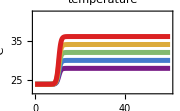
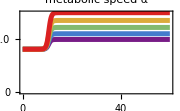
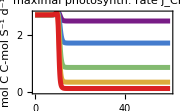
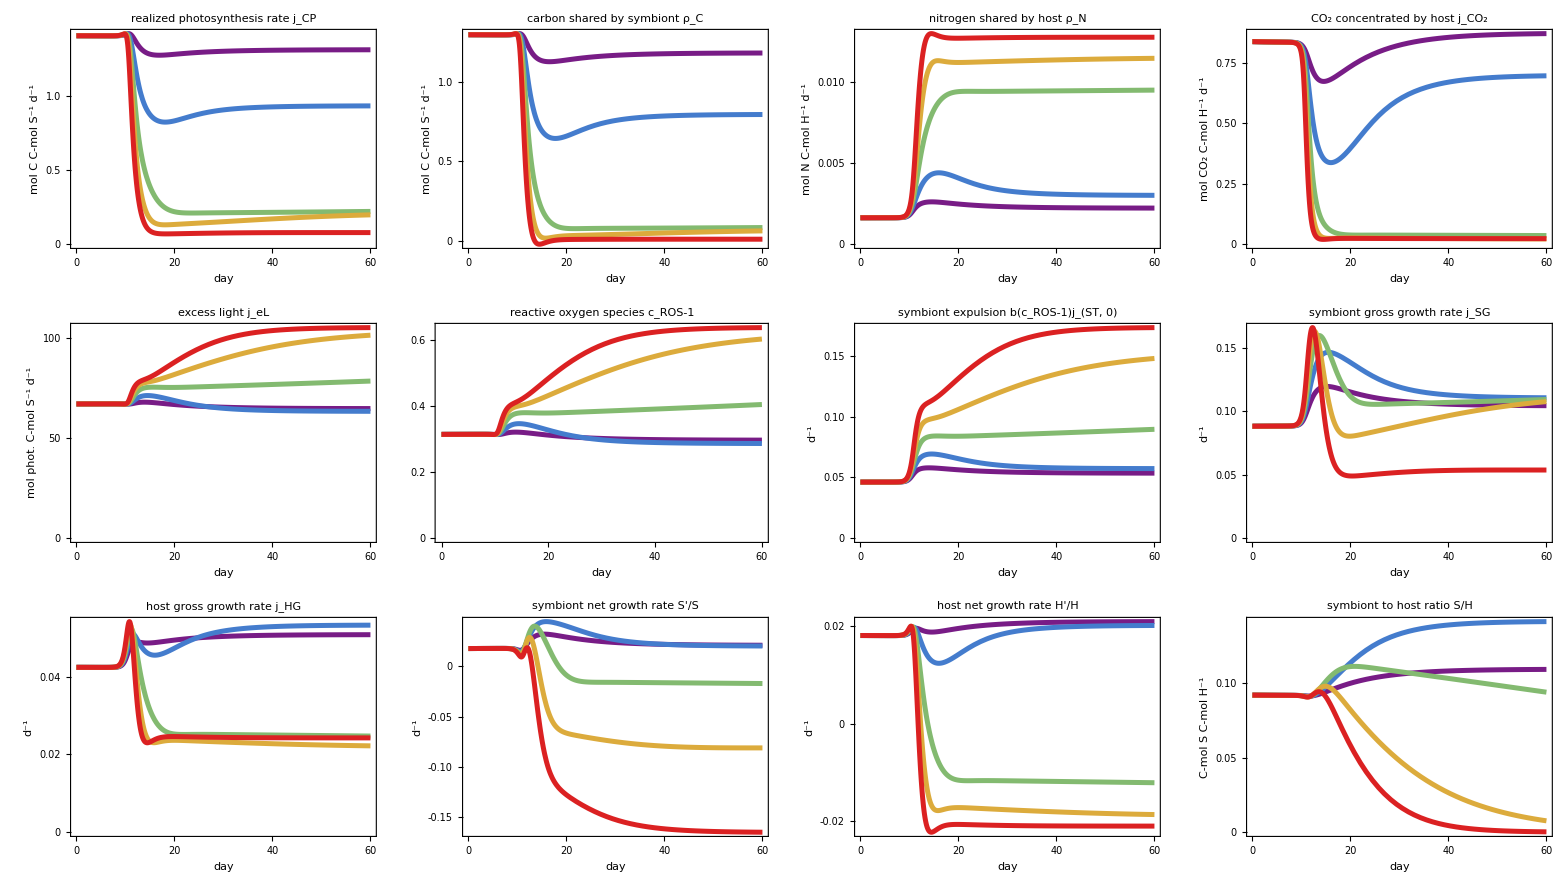
-Graphics-peak temperature
-Graphics- | 28°C
-Graphics- | 30°C
-Graphics- | 32°C
-Graphics- | 34°C
-Graphics- | 36°C
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-

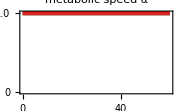
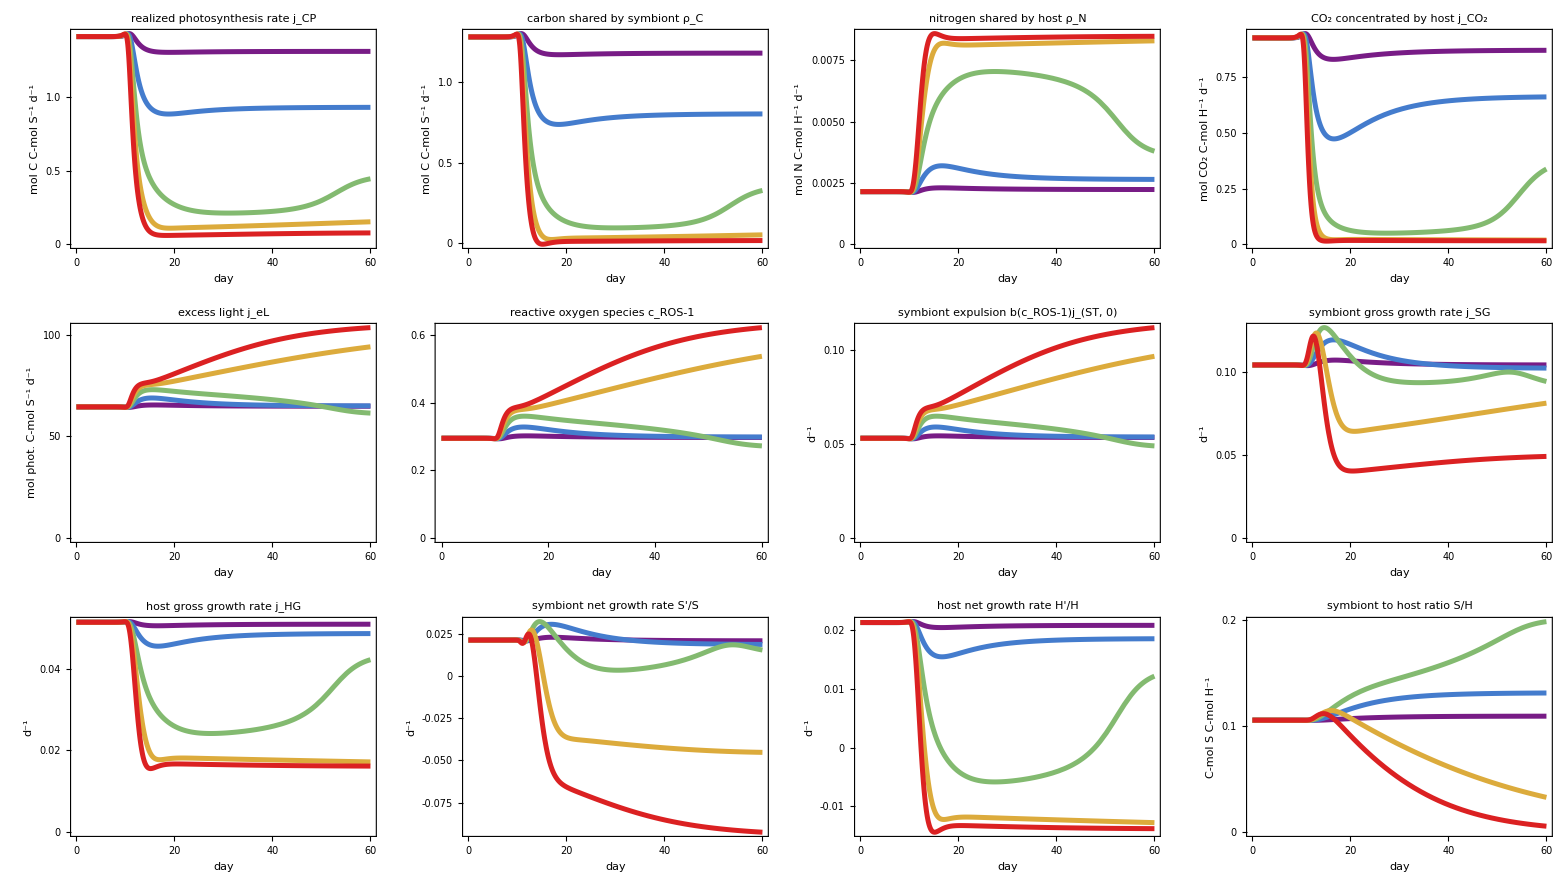
-Graphics-peak temperature
-Graphics- | 28°C
-Graphics- | 30°C
-Graphics- | 32°C
-Graphics- | 34°C
-Graphics- | 36°C
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-

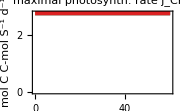
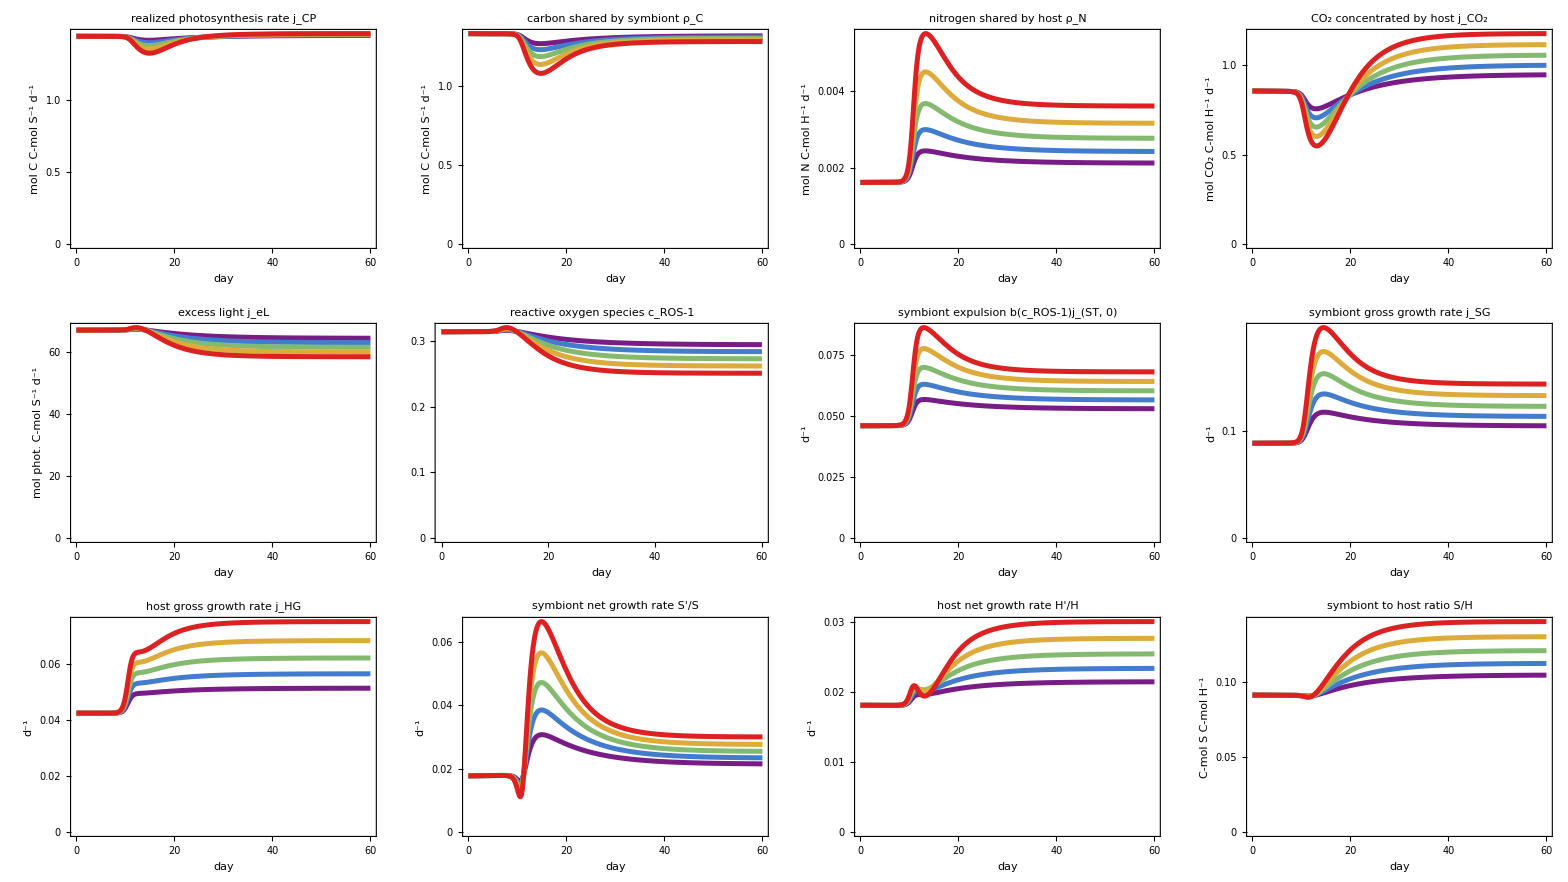
-Graphics-peak temperature
-Graphics- | 28°C
-Graphics- | 30°C
-Graphics- | 32°C
-Graphics- | 34°C
-Graphics- | 36°C
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-

```mathematica
numberupruns=5;
upenvironments=Table[environmentup[24,26+2i],{i,numberupruns}];
uptimes=((tmax->_)->(tmax->60));
wrangeup={w->{22,42}};
(Export[NotebookDirectory[]<>"export/"<>"simus-up-FvFm-Arr-many-temperatures.pdf",#];#)&@PanelPlotMultipleRuns[toplot,parvalsFvFmArr/.uptimes,upenvironments,Evaluate@{PlotStyle->Table[{Thickness[0.02],ColorData["Rainbow"][(i-1)/(numberupruns-1)]},{i,numberupruns}]},inivalsdefault,{-100,-99},wrangeup,arrangementMultipleRuns]
(Export[NotebookDirectory[]<>"export/"<>"simus-up-FvFm-many-temperatures.pdf",#];#)&@PanelPlotMultipleRuns[toplot,parvalsFvFm/.uptimes,upenvironments,Evaluate@{PlotStyle->Table[{Thickness[0.02],ColorData["Rainbow"][(i-1)/(numberupruns-1)]},{i,numberupruns}]},inivalsdefault,{-100,-99},wrangeup,arrangementMultipleRuns]
(Export[NotebookDirectory[]<>"export/"<>"simus-up-Arr-many-temperatures.pdf",#];#)&@PanelPlotMultipleRuns[toplot,parvalsArr/.uptimes,upenvironments,Evaluate@{PlotStyle->Table[{Thickness[0.02],ColorData["Rainbow"][(i-1)/(numberupruns-1)]},{i,numberupruns}]},inivalsdefault,{-100,-99},wrangeup,arrangementMultipleRuns]
```

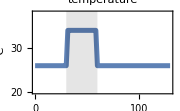
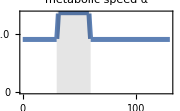
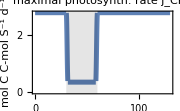
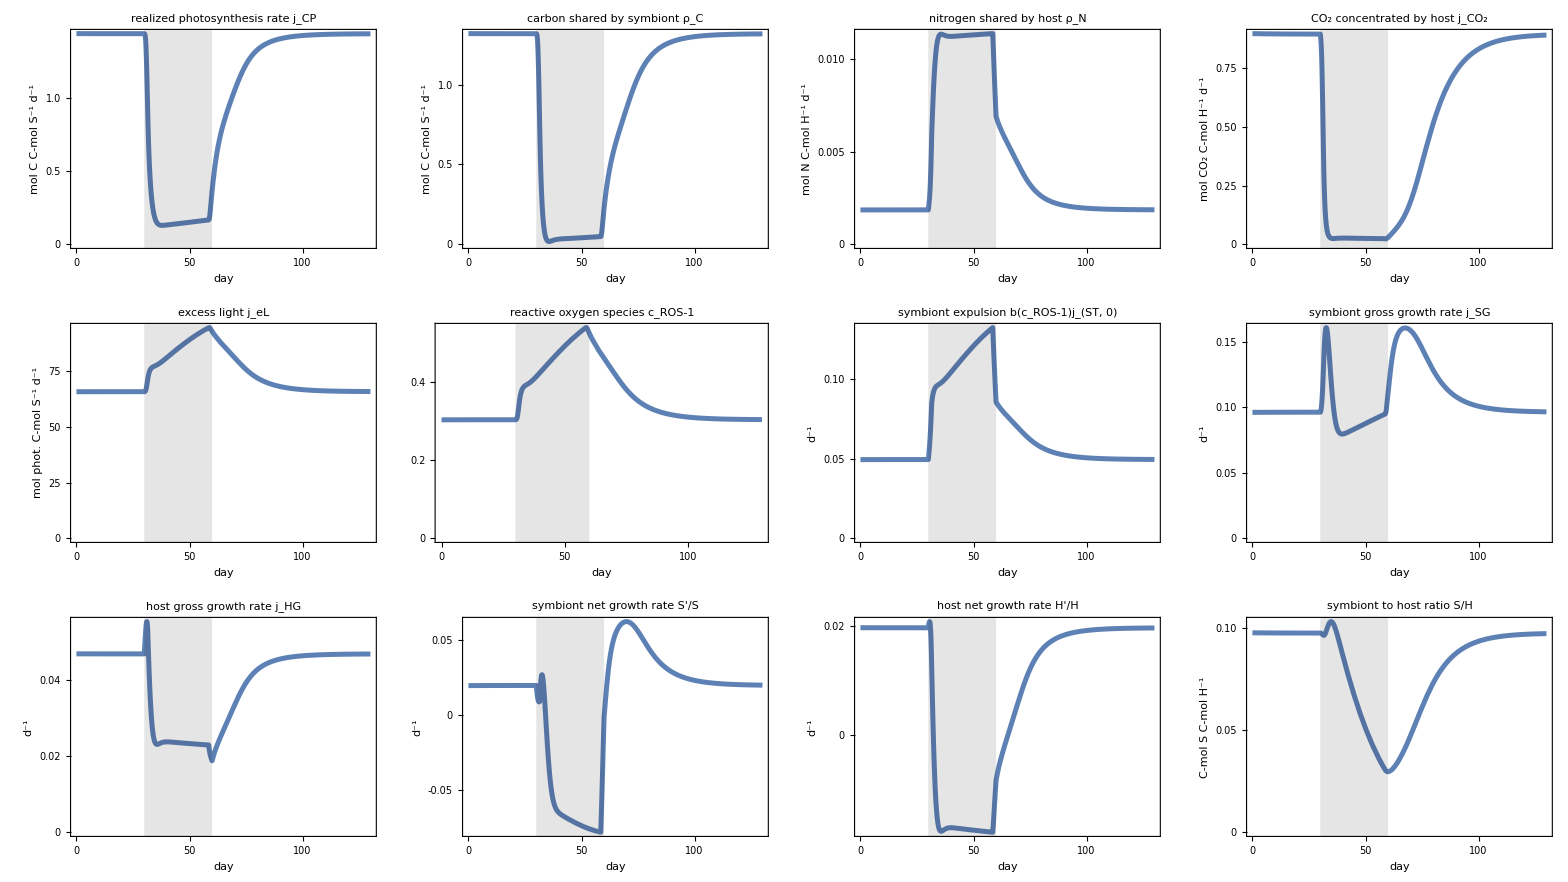
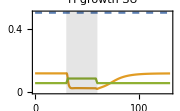
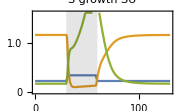
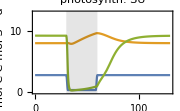
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
increase[txs_]:=Piecewise[Join[Table[{txs[[i,2]]+(txs[[i+1,2]]-txs[[i,2]])((t-txs[[i,1]])/(txs[[i+1,1]]-txs[[i,1]])),t<txs[[i+1,1]]},{i,1,Length[txs]-1}],{{txs[[-1,2]],True}}]];
wrangeUpDown={w->{20,38}};

updowntimes={30,60};
updownshades=updowntimes;
updownmin=26;
updownmax=34;
environmentupdown={w->increase[{{"NA",updownmin},{updowntimes[[1]],updownmin},{updowntimes[[1]]+1.5,updownmax},{updowntimes[[2]]-1.5,updownmax},{updowntimes[[2]],updownmin}}]};



(*environmentupdown={w->Piecewise[{{32, updowntimes[[1]]<t<updowntimes[[2]]}, {26, True}}]};*)
PWplot["simus-updown-no-hysteresis-FvFm-Arr.pdf",parvalsFvFmArr/.(tmax->_)->(tmax->130),environmentupdown,Join[{H->#,S->.2#}&@(4{.1,10}),wrangeUpDown,SUmaxs],updownshades]
```

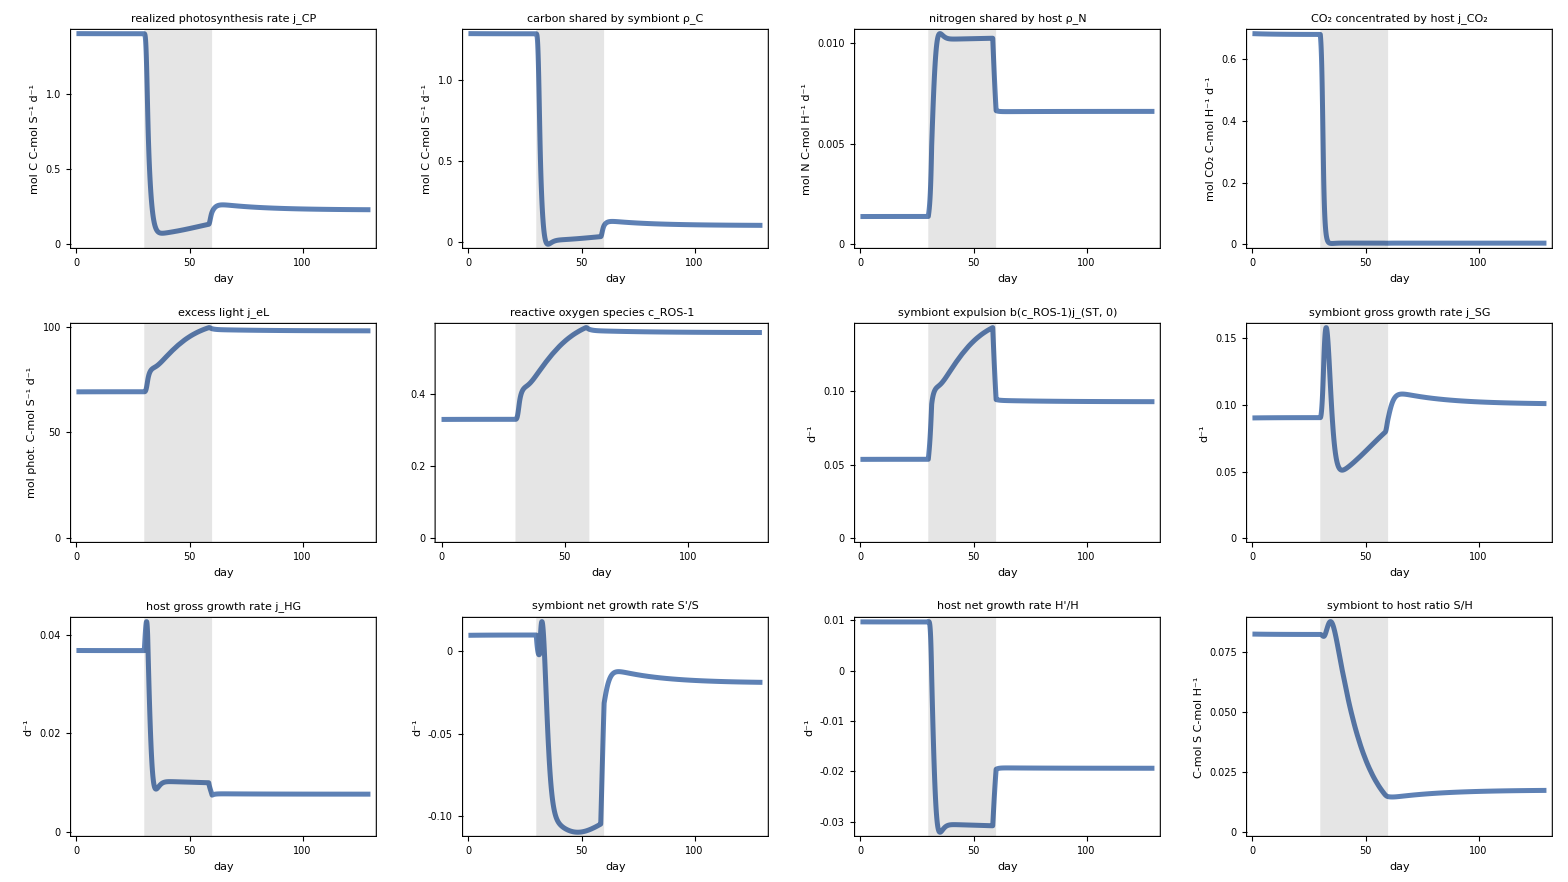
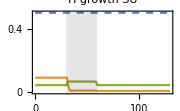
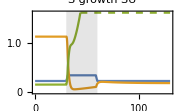
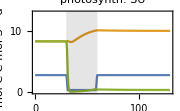
-Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
PWplot["simus-updown-hysteresis-FvFm-Arr.pdf",parvalsFvFmArr/.{(X->_)->(X->7.5 10^-8),(tmax->_)->(tmax->130)},environmentupdown,Join[{H->#,S->.2#}&@({.01,10}),wrangeUpDown,SUmaxs],updownshades]
```